# Calculation of eikonal corrections at KE = 100 MeV

9/19/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];
```

```mathematica
(*pp100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100b.csv"];*)
```

```mathematica
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],(pp100a[[All,2]]+pp100b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp100=θtoq/@θpp100;
```

```mathematica
pn100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100b.csv"];
```

```mathematica
(*pn100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100b.csv"];*)
```

```mathematica
pn100a=Transpose[{pn100a[[All,1]],pn100a[[All,2]]+I*pn100a[[All,3]]}];
pn100b=Transpose[{pn100b[[All,1]],pn100b[[All,2]]+I*pn100b[[All,3]]}];
```

```mathematica
θpn100=Transpose[{pn100a[[All,1]],(pn100a[[All,2]]+pn100b[[All,2]])/2}];
```

```mathematica
pn100=θtoq/@θpn100;
```

```mathematica
NN100=(pp100+pn100)/2;
```

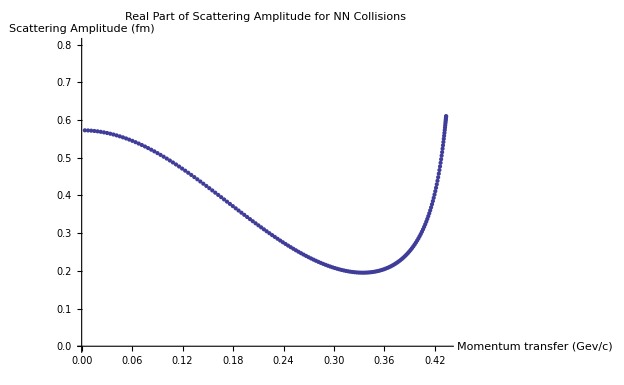

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Re[NN100[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

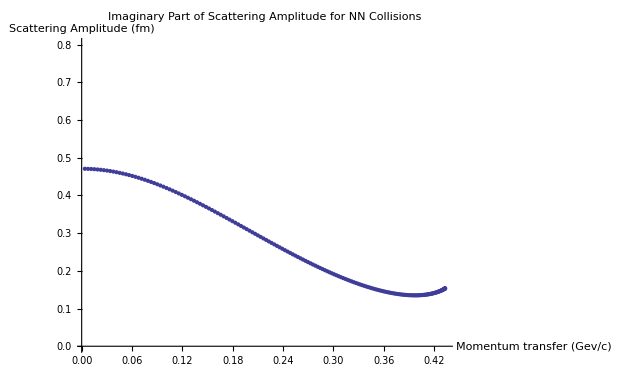

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Im[NN100[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

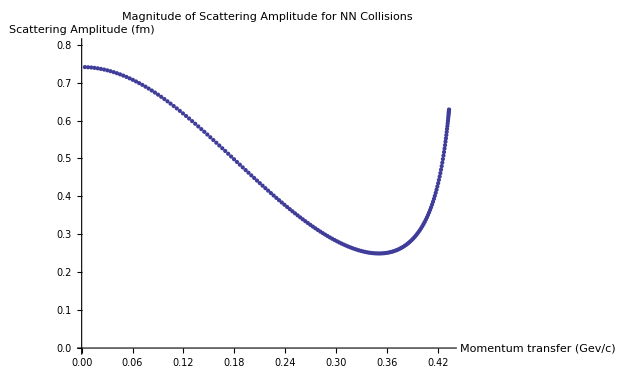

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

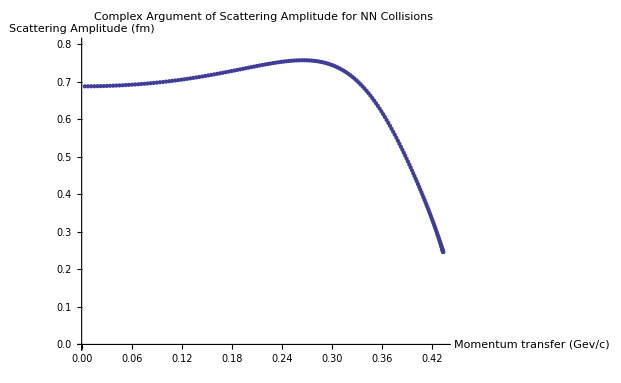

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.740121,βre→12.3977}

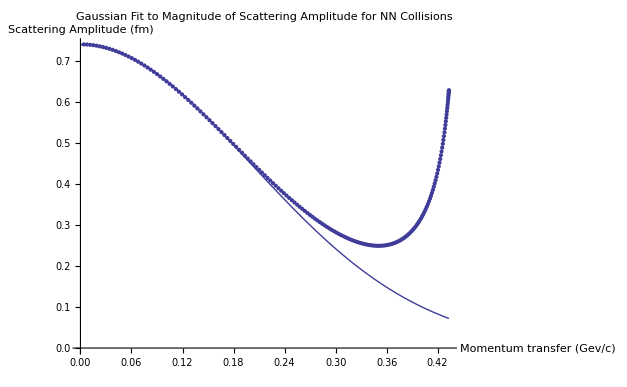

```mathematica
Npts=50;
FindFit[Transpose[{NN100[[1;;Npts,1]],Abs[NN100[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→1.21713,βim→-1.26645}

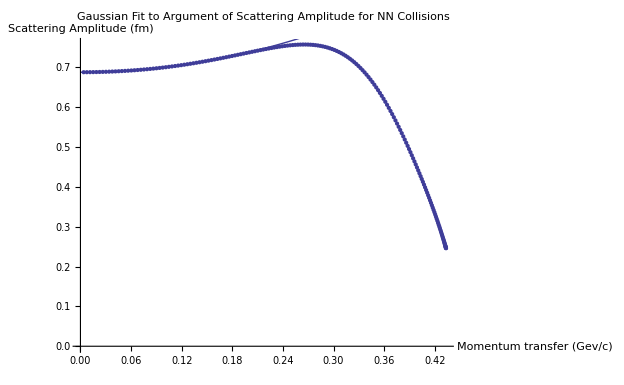

```mathematica
FindFit[Transpose[{NN100[[1;;Npts,1]],Arg[NN100[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.7401208259427848&&ρ==1.217127351734708,{σ,ρ}]
```

{{σ→5.37714,ρ→1.21713}}

Fitted parameters:

```mathematica
σ=5.377143967540269;
ρ=1.217127351734708;
β=12.39772991491029-1.2664454506269087 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-0.493154+0.489051 ⅈ

```mathematica
F0100[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0100[0]]
```

217.136

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

-0.493154+0.489051 ⅈ

```mathematica
Clear[U100]
```

```mathematica
Utemp[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U100=Quiet[Interpolation[Table[{q,Utemp[q]},{q,0,2 κ,.01}]]];
```

```mathematica
U100[0]
```

68.7392+68.011 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

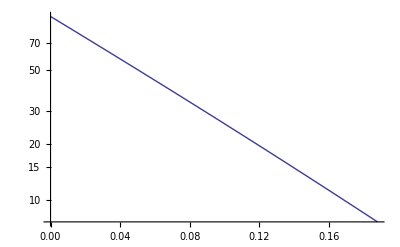

```mathematica
Quiet[LogPlot[Abs[U100[Sqrt[q]]],{q,0,(2 κ)^2}]]
```

The magnitude seems to be well approximated by a gaussian.

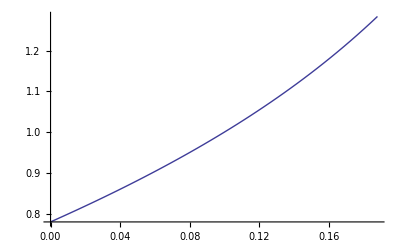

```mathematica
Quiet[Plot[Arg[U100[Sqrt[q]]],{q,0,(2 κ)^2}]]
```

```mathematica
Quiet[U100[.1]]
```

59.1488+60.8189 ⅈ

```mathematica
γ=100*Quiet[(Log[U100[0]]-Log[U100[0.1]])]
```

13.0851-1.92459 ⅈ

```mathematica
Z=U100[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.885258+0.081938 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+γ/2)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1100[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+γ))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1100[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1100[0]+FD1100[0]]/Im[F0100[0]+FO1100[0]+FD1100[0]]
```

0.00295068

The first order correction is about 0.3% at 100 MeV.

```mathematica
40*Pi/(k/ℏc) Im[F0100[0]]
40*Pi/(k/ℏc) Im[FO1100[0]+FD1100[0]]
40*Pi/(k/ℏc) Im[FO1100[0]+FD1100[0]+F0100[0]]
```

217.136

0.642597

217.779

```mathematica
FO1100[0]
```

-0.0101509+0.0870332 ⅈ

```mathematica
FD1100[0]
```

-0.0123339-0.0779682 ⅈ

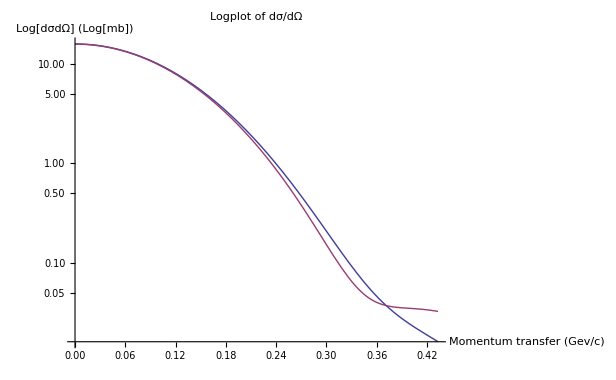

```mathematica
LogPlot[{Abs[F0100[q]]^2,Abs[F0100[q]+FO1100[q]+FD1100[q]]^2},{q,0,2 κ},PlotLabel->"Logplot of dσ/dΩ",AxesLabel->{"Momentum transfer (Gev/c)","Log[dσdΩ] (Log[mb])"}]
```